```mathematica
<<xACT`xTensor`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2018, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.3, {2018,2,28}

CopyRight (C) 2002-2018, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
<<xACT`xPert`
```

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2018, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

```mathematica
<<xACT`xTras`
```

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2018, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.4, {2018,2,28}

CopyRight (C) 2005-2018, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.4, {2016,11,29}

CopyRight (C) 2011-2016, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M4, 4, {a,b,c,d,e,f,i,k,l,m,n}]
```

** DefManifold: Defining manifold M4.

** DefVBundle: Defining vbundle TangentM4.

```mathematica
DefMetricPerturbation/.Options@DefMetric
```

True

```mathematica
DefMetric[1, η[-a,-b],CD,{"%","∇"}]
```

** DefTensor: Defining symmetric metric tensor η[-a,-b].

** DefTensor: Defining antisymmetric tensor epsilonη[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetraη[-a,-b,-c,-d].

** DefTensor: Defining tetrametric Tetraη†[-a,-b,-c,-d].

** DefCovD: Defining covariant derivative CD[-a].

** DefTensor: Defining vanishing torsion tensor TorsionCD[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelCD[a,-b,-c].

** DefTensor: Defining Riemann tensor RiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Ricci tensor RicciCD[-a,-b].

** DefCovD:  Contractions of Riemann automatically replaced by Ricci.

** DefTensor: Defining Ricci scalar RicciScalarCD[].

** DefCovD:  Contractions of Ricci automatically replaced by RicciScalar.

** DefTensor: Defining symmetric Einstein tensor EinsteinCD[-a,-b].

** DefTensor: Defining Weyl tensor WeylCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric TFRicci tensor TFRicciCD[-a,-b].

** DefTensor: Defining Kretschmann scalar KretschmannCD[].

** DefCovD:  Computing RiemannToWeylRules for dim 4

** DefCovD:  Computing RicciToTFRicci for dim 4

** DefCovD:  Computing RicciToEinsteinRules for dim 4

** DefTensor: Defining symmetrized Riemann tensor SymRiemannCD[-a,-b,-c,-d].

** DefTensor: Defining symmetric Schouten tensor SchoutenCD[-a,-b].

** DefTensor: Defining symmetric cosmological Schouten tensor SchoutenCCCD[LI[_],-a,-b].

** DefTensor: Defining symmetric cosmological Einstein tensor EinsteinCCCD[LI[_],-a,-b].

** DefTensor: Defining weight +2 density Detη[]. Determinant.

** DefParameter: Defining parameter PerturbationParameterη.

** DefTensor: Defining tensor Perturbationη[LI[order],-a,-b].

```mathematica
η[-a,-b]η[a,b]
```

4

```mathematica
DefMetricPerturbation[η,h,ϵ]
```

** DefParameter: Defining parameter ϵ.

** DefTensor: Defining tensor h[LI[order],-a,-b].

```mathematica
h[LI[2],-a,-b]
```

h | 2 |   |  
  | a | b

```mathematica
Perturbed[η[a,b],1]//ExpandPerturbation
```

-ϵ h | 1 | a | b
  |   |  +η | a | b
  |

```mathematica
Sqrt[-Detη[]]*Perturbed[η[m,n],1]//ExpandPerturbation
```

√(-η^OverTilde[~]) (-ϵ h | 1 | m | n
  |   |  +η | m | n
  |  )

```mathematica
Perturbation[RicciCD[-m,-n],1]//ExpandPerturbation//ContractMetric//Simplification//SortCovDs
```

1/2 (-∇_a ∇^a h | 1 |   |  
  | m | n+∇_a ∇_m h | 1 |   | a
  | n |  +∇_a ∇_n h | 1 |   | a
  | m |  -∇_n ∇_m h | 1 | a |  
  |   | a)

```mathematica
R :=η[m,n]*Perturbation[RicciCD[-m,-n],1]//ExpandPerturbation//ContractMetric//Simplification//SortCovDs
```

```mathematica
R
```

∇_n ∇_m h | 1 | m | n
  |   |  -∇_n ∇^n h | 1 | m |  
  |   | m

```mathematica
η[a,b]h[-a,-b]//ContractMetric
```

h |   | a
a |

```mathematica
CD[-n][η[m,n]h[-m,-n]//ContractMetric]
```

∇_n h |   | m
m |

```mathematica
CD[-n][h[c,-c]]
```

∇_n h | c |  
  | c

```mathematica
CD[-n][h]
```

∇_n h

```mathematica
Lag:=(1/2)*((CD[-m][h[LI[1],m,n]])*(CD[-n][h[LI[1],-c,c]]) - (CD[-m][h[LI[1],c,d]])*(CD[-c][h[LI[1],m,-d]]) + (1/2)*η[m,n]*(CD[-m][h[LI[1],c,d]])*(CD[-n][h[LI[1],-c,-d]])-(1/2)*η[m,n]*(CD[-m][h[LI[1],c,-c]])*(CD[-n][h[LI[1],d,-d]]))
```

```mathematica
Lag
```

1/2 (-∇_c h | 1 | m |  
  |   | d ∇_m h | 1 | c | d
  |   |  +∇_m h | 1 | m | n
  |   |   ∇_n h | 1 |   | c
  | c |  +1/2 η | m | n
  |   ∇_m h | 1 | c | d
  |   |   ∇_n h | 1 |   |  
  | c | d-1/2 η | m | n
  |   ∇_m h | 1 | c |  
  |   | c ∇_n h | 1 | d |  
  |   | d)

```mathematica
(VarD[h[LI[1],c,d],CD][Lag*Sqrt[-Detη[]]]/Sqrt[-Detη[]])/.delta[-LI[1],LI[1]]-> 1//ExpandPerturbation//ContractMetric//ToCanonical
```

-1/2 ∇_a ∇^a h | 1 |   |  
  | c | d+1/2 ∇_a ∇_c h | 1 |   | a
  | d |  +1/2 ∇_a ∇_d h | 1 |   | a
  | c |  -1/2 η |   |  
c | d ∇_b ∇_a h | 1 | a | b
  |   |  +1/2 η |   |  
c | d ∇_b ∇^b h | 1 | a |  
  |   | a-1/4 ∇_c ∇_d h | 1 | a |  
  |   | a-1/4 ∇_d ∇_c h | 1 | a |  
  |   | a

```mathematica
CD[c][(VarD[h[LI[1],c,d],CD][Lag*Sqrt[-Detη[]]]/Sqrt[-Detη[]])]/.delta[-LI[1],LI[1]]-> 1//ExpandPerturbation//ContractMetric//ToCanonical//Simplification
```

1/4 (-∇_a ∇^a ∇_d h | 1 | c |  
  |   | c+2 ∇_a ∇_c ∇^a h | 1 |   | c
  | d |  +2 ∇_a ∇_c ∇_d h | 1 | c | a
  |   |  -∇_a ∇_d ∇^a h | 1 | c |  
  |   | c-2 ∇_c ∇_a ∇^a h | 1 |   | c
  | d |  +2 ∇_d ∇_a ∇^a h | 1 | c |  
  |   | c-2 ∇_d ∇_a ∇_c h | 1 | c | a
  |   |  )

```mathematica
η[c,d](VarD[h[LI[1],c,d],CD][Lag*Sqrt[-Detη[]]]/Sqrt[-Detη[]])/.delta[-LI[1],LI[1]]-> 1//ExpandPerturbation//ContractMetric//ToCanonical
```

-∇_d ∇_c h | 1 | c | d
  |   |  +∇_d ∇^d h | 1 | c |  
  |   | c

```mathematica
DefTensor[t[n],M4]
```

** DefTensor: Defining tensor t[n].

```mathematica
DefTensor[H[-m,-n],M4]
```

** DefTensor: Defining tensor H[-m,-n].

```mathematica
(CD[-l][CD[m][t[n]]])*(CD[l][H[-m,-n]])//ExpandPerturbation
```

∇_l ∇^m t | n
  ∇^l H |   |  
m | n

```mathematica
DefTensor[T[m,n],M4]
```

** DefTensor: Defining tensor T[m,n].

```mathematica
DefConstantSymbol[G]
```

** DefConstantSymbol: Defining constant symbol G.

```mathematica
LagEff := (1/2)*( (1/(32*Pi*G))*(CD[-l][h[LI[1],m,n]]*CD[l][h[LI[1],-m,-n]] - (1/2)*CD[-l][h[LI[1],a,-a]]*CD[l][h[LI[1],b,-b]]) - h[LI[1],-m,-n]*T[m,n] )
```

```mathematica
LagEff
```

1/2 (-h | 1 |   |  
  | m | n T | m | n
  |  +(-1/2 ∇_l h | 1 | a |  
  |   | a ∇^l h | 1 | b |  
  |   | b+∇_l h | 1 | m | n
  |   |   ∇^l h | 1 |   |  
  | m | n)/(32 G π))

```mathematica
(VarD[h[LI[1],c,d],CD][LagEff*Sqrt[-Detη[]]]/Sqrt[-Detη[]])==0/.delta[-LI[1],LI[1]]-> 1//ExpandPerturbation//ContractMetric//ToCanonical
```

-1/4 T |   |  
c | d-(T |   |  
d | c)/4-(∇_a ∇^a h | 1 |   |  
  | c | d)/(32 G π)+(η |   |  
c | d ∇_b ∇^b h | 1 | a |  
  |   | a)/(64 G π)==0

```mathematica
DefConstantSymbol[M]
```

** DefConstantSymbol: Defining constant symbol M.

```mathematica
DefConstantSymbol[A]
```

** DefConstantSymbol: Defining constant symbol A.

```mathematica
LagFP:=((CD[-m][h[LI[1],m,n]])*(CD[-n][h[LI[1],-c,c]]) - (CD[-m][h[LI[1],c,d]])*(CD[-c][h[LI[1],m,-d]]) + (1/2)*η[m,n]*(CD[-m][h[LI[1],c,d]])*(CD[-n][h[LI[1],-c,-d]])-(1/2)*η[m,n]*(CD[-m][h[LI[1],c,-c]])*(CD[-n][h[LI[1],d,-d]])) - (1/2)*M^2*(h[LI[1],m,n]*h[LI[1],-m,-n] - (1-A)h[LI[1],c,-c]*h[LI[1],d,-d])
```

```mathematica
LagFP
```

-1/2 M^2 (-(1-A) h | 1 | c |  
  |   | c h | 1 | d |  
  |   | d+h | 1 |   |  
  | m | n h | 1 | m | n
  |   |  )-∇_c h | 1 | m |  
  |   | d ∇_m h | 1 | c | d
  |   |  +∇_m h | 1 | m | n
  |   |   ∇_n h | 1 |   | c
  | c |  +1/2 η | m | n
  |   ∇_m h | 1 | c | d
  |   |   ∇_n h | 1 |   |  
  | c | d-1/2 η | m | n
  |   ∇_m h | 1 | c |  
  |   | c ∇_n h | 1 | d |  
  |   | d

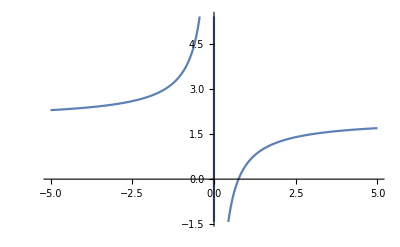

```mathematica
Plot[-(3-4x)/(2x),{x,-5,5}]
```